```mathematica
BinCounts
```

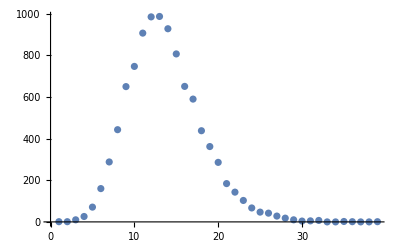

```mathematica
ListPlot[BinCounts[Table[Max[RandomVariate[NormalDistribution[],100]],10000],.1]]
```

```mathematica
PDF[GumbelDistribution[a,b],x]
```

(ⅇ^(-ⅇ^((-a+x)/b)+(-a+x)/b))/b

```mathematica
Manipulate[Plot[(ⅇ^(-ⅇ^((-a-x)/b)+(-a-x)/b))/b,{x,0,100}, PlotRange->All],{a,0,100},{b,0.01,10}]
```

```mathematica
NonlinearModelFit[BinCounts[Table[Max[RandomVariate[NormalDistribution[],100]],10000],.1],(ⅇ^(-ⅇ^((-a+x)/b)+(-a+x)/b))/b,{{a,0.1},{b,0.1}},x]
```

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

FittedModel[10. ⅇ^(-ⅇ^(10. (-0.1+x))+10. (-0.1+x))]

```mathematica
?NonlinearModelFit
```